```mathematica
numSeg = 10;
timeIntegratorLists = {"Newmark", "TRBDF2"};
segList = {10, 50, 100};
powList = {"10", "20", "40", "80"};
folderPrefix = "/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_";
folderSufix = "/ConstantYoungs/LinearElements/impulse_mag_";
alphaLists = {};
For[j = 1, j≤ Length[segList],
alphaListsj = {}; 
For[p = 1, p ≤ Length[powList], 
alphaListsjp = {}; 
For[i=1, i≤ Length[timeIntegratorLists],
alphaListsjpi = {};
folderName= folderPrefix <> ToString[segList[[j]]] <>folderSufix <>powList[[p]] <>"_pow_" <> powList[[p]]<>"/"<> timeIntegratorLists[[i]] <>"/";
Print[{j , p, i, folderName}];
For[k =1,k≤ segList[[j]], 
alphaList = Import[folderName <> "alpha_" <> ToString[k - 1] <> ".txt", "List"];
AppendTo[alphaListsjpi, alphaList];
k++];
alphaPlots = ListLinePlot[Table[Table[{(l -1)* 0.05, alphaListsjpi[[m]][[l]]}, {l, 1, Length[alphaListsjpi[[m]]]}], {m, segList[[j]] - 9, segList[[j]]}], ImageSize->Large, PlotRange->All, PlotStyle->{Thickness[0.001]}, PlotLegends-> Union[Table["the " <> ToString[10 - m]<> "th smallest eval", {m, 0, 6}], {"the smallest eval", "the 2nd smallest eval", "the 3rd smallest eval"}]];
Export[folderName <> "alphas_plots_" <>ToString[segList[[j]]] <> "_" <> powList[[p]] <> ".png", alphaPlots];
AppendTo[alphaListsjp, alphaListsjpi];
i++];
AppendTo[alphaListsj, alphaListsjp];
p++];
  AppendTo[ alphaLists, alphaListsj];
j++];
```

{1,1,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_10/ConstantYoungs/LinearElements/impulse_mag_10_pow_10/Newmark/}

{1,1,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_10/ConstantYoungs/LinearElements/impulse_mag_10_pow_10/TRBDF2/}

{1,2,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_10/ConstantYoungs/LinearElements/impulse_mag_20_pow_20/Newmark/}

{1,2,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_10/ConstantYoungs/LinearElements/impulse_mag_20_pow_20/TRBDF2/}

{1,3,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_10/ConstantYoungs/LinearElements/impulse_mag_40_pow_40/Newmark/}

{1,3,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_10/ConstantYoungs/LinearElements/impulse_mag_40_pow_40/TRBDF2/}

{1,4,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_10/ConstantYoungs/LinearElements/impulse_mag_80_pow_80/Newmark/}

{1,4,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_10/ConstantYoungs/LinearElements/impulse_mag_80_pow_80/TRBDF2/}

{2,1,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_50/ConstantYoungs/LinearElements/impulse_mag_10_pow_10/Newmark/}

{2,1,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_50/ConstantYoungs/LinearElements/impulse_mag_10_pow_10/TRBDF2/}

{2,2,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_50/ConstantYoungs/LinearElements/impulse_mag_20_pow_20/Newmark/}

{2,2,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_50/ConstantYoungs/LinearElements/impulse_mag_20_pow_20/TRBDF2/}

{2,3,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_50/ConstantYoungs/LinearElements/impulse_mag_40_pow_40/Newmark/}

{2,3,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_50/ConstantYoungs/LinearElements/impulse_mag_40_pow_40/TRBDF2/}

{2,4,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_50/ConstantYoungs/LinearElements/impulse_mag_80_pow_80/Newmark/}

{2,4,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_50/ConstantYoungs/LinearElements/impulse_mag_80_pow_80/TRBDF2/}

{3,1,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_100/ConstantYoungs/LinearElements/impulse_mag_10_pow_10/Newmark/}

{3,1,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_100/ConstantYoungs/LinearElements/impulse_mag_10_pow_10/TRBDF2/}

{3,2,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_100/ConstantYoungs/LinearElements/impulse_mag_20_pow_20/Newmark/}

{3,2,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_100/ConstantYoungs/LinearElements/impulse_mag_20_pow_20/TRBDF2/}

{3,3,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_100/ConstantYoungs/LinearElements/impulse_mag_40_pow_40/Newmark/}

{3,3,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_100/ConstantYoungs/LinearElements/impulse_mag_40_pow_40/TRBDF2/}

{3,4,1,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_100/ConstantYoungs/LinearElements/impulse_mag_80_pow_80/Newmark/}

{3,4,2,/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.050000_1.000000_numSeg_100/ConstantYoungs/LinearElements/impulse_mag_80_pow_80/TRBDF2/}

```mathematica
Length[alphaLists[[1]][[1]][[1]]]
```

10

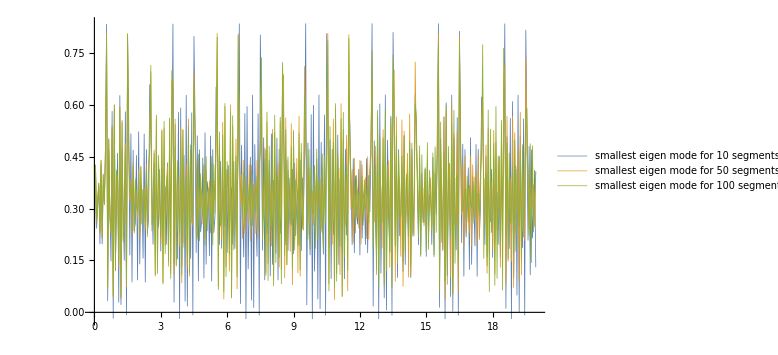

```mathematica
ListLinePlot[Table[Table[{(i -1)* 0.05, alphaLists[[j]][[4]][[1]][[segList⟦j⟧]][[i]]}, {i, 1, Length[alphaLists[[j]][[4]][[1]][[ segList⟦j⟧ ]]]}], {j, 1, Length[segList]}], ImageSize->Large, PlotRange->All, PlotStyle->{Thickness[0.001]}, PlotLegends-> Table["smallest eigen mode for " <>ToString[segList⟦s⟧] <> " segments", {s, 1, Length[segList]}]]
```

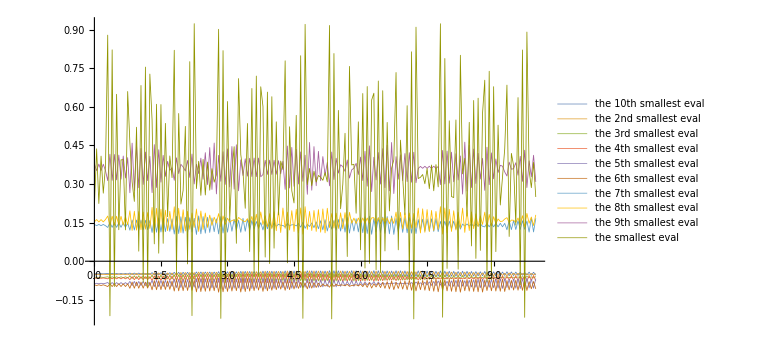

```mathematica
ClearAll;
alphaListsjpi = {};
For[k =1,k≤ segList[[3]], 
alphaList = Import["/home/zchen96/Projects/TimeIntegrator/build_clion/output/Harmonic1d/0.100000_1.000000_numSeg_100/ConstantYoungs/LinearElements/impulse_mag_80_pow_80/Newmark/" <>"alpha_" <> ToString[k - 1] <> ".txt", "List"];
AppendTo[alphaListsjpi, alphaList];
k++];
ListLinePlot[Table[Table[{(l -1)* 0.05, alphaListsjpi[[m]][[l]]}, {l, 1, Length[alphaListsjpi[[m]]]}], {m, segList[[3]] - 9, segList[[3]]}], ImageSize->Large, PlotRange->All, PlotStyle->{Thickness[0.001]}, PlotLegends-> Union[Table["the " <> ToString[10 - m]<> "th smallest eval", {m, 0, 6}], {"the smallest eval", "the 2nd smallest eval", "the 3rd smallest eval"}]]
```

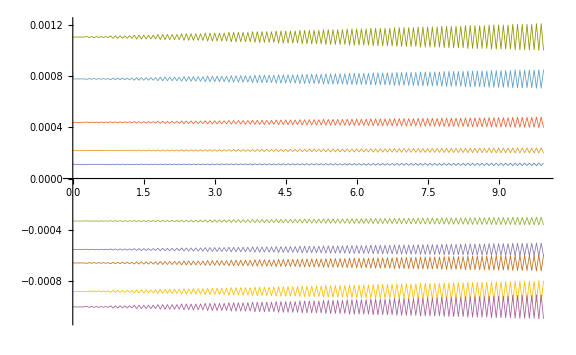

```mathematica
ListLinePlot[Table[Table[{(l -1)* 0.05, alphaListsjpi[[m]][[l]]}, {l, 1, Length[alphaListsjpi[[m]]]}], {m, 1, 10}], ImageSize->Large, PlotRange->All, PlotStyle->{Thickness[0.001]}]
```